### Auxiliary functions

```mathematica
balance[quiver_]:=quiver[[1]].quiver[[2]];
clean[quiver_]:=Module[{nonzero},
nonzero=Select[Range[Length[quiver[[2]]]],quiver[[2,#]]>0&];
{quiver[[1]][[nonzero,nonzero]],quiver[[2]][[nonzero]]}
];
divideDiagonal[mat_]:=mat-1/2*DiagonalMatrix[Diagonal[mat]];
plot[quiver_]:=If[quiver=={{},{}},"",Module[{b},AdjacencyGraph[quiver[[1]]+2IdentityMatrix[Length[quiver[[2]]]]//divideDiagonal,VertexLabels->Table[i->quiver[[2,i]],{i,1,Length[quiver[[2]]]}],VertexStyle->Table[i->{b=balance[quiver][[i]];If[b>0,Blue,If[b==0,Green,Red]]},{i,1,Length[quiver[[2]]]}],VertexSize->.1]]];

lengthNodes[mat_]:=Module[{nn},
nn=Length[mat];
Table[Subscript[x, i],{i,1,nn}]/.Solve[Join[{Subscript[x, 1]==1},Flatten[Table[If[mat[[i,j]]≠0,mat[[i,j]]/mat[[j,i]]==Subscript[x, i]/Subscript[x, j],1==1],{i,1,nn},{j,1,nn}]]],Table[Subscript[x, i],{i,1,nn}]][[1]]
];

longNodes[mat_]:=Module[{len,max},
len=lengthNodes[mat];
max=Max[len];
Select[Range[Length[mat]],len[[#]]==max&]
];

isInstModSpace[quiver_]:=Module[{delta,aux,gcd,intersection},(0==(Times@@Table[If[quiver[[2,i]]>0,
delta=Table[KroneckerDelta[j,i],{j,1,Length[quiver[[2]]]}];
aux=(quiver[[2]]-delta);
gcd=GCD@@aux;
intersection=(aux.(quiver[[1]]).(delta));
If[zeroQ[(quiver[[1]].aux)*aux]&&intersection==gcd,0,1],1],{i,longNodes[quiver[[1]]]}]))
];
positiveQ[x_]:=(Abs[x]==x);
zeroQ[x_]:=(Abs[x]==-Abs[x]);
positiveQStrict[x_]:=(Abs[x]==x)&&Not[x==-x];
numberCommonElements[list1_,list2_]:=Length[Flatten[ConstantArray[#,Min[Count[list1,#],Count[list2,#]]]&/@Intersection[list1,list2],1]];
elementarize[matrix_]:=Module[{nn},
nn=Length[matrix];
Table[If[Or@@Table[matrix[[i,k]]==1&&matrix[[k,j]]==1,{k,1,nn}],0,matrix[[i,j]]],{i,1,nn},{j,1,nn}]
];
descends[leaf1_,leaf2_]:=Module[{aux1,aux2},
(Length[leaf2]==Length[leaf1]&&(numberCommonElements[leaf1,leaf2]==Length[leaf1]-1)&&positiveQ[Total[leaf1]-Total[leaf2]])||(Length[leaf2]==Length[leaf1]-1&&(numberCommonElements[leaf1,leaf2]==Length[leaf1]-1)&&positiveQ[Total[leaf1]-Total[leaf2]])||(Length[leaf2]==Length[leaf1]+1&&(numberCommonElements[leaf1,leaf2]==Length[leaf1]-1)&&positiveQ[Total[leaf1]-Total[leaf2]])
];
multiplicityElementaryTransition[leaf1_,leaf2_]:=Module[{},
t1=Tally[leaf1];
t2=Tally[leaf2];
Select[t1,Not[MemberQ[t2,#]]&][[1,2]]
];
```

### Fission and Decay code

```mathematica
level1Descendents[mat_,ranks_]:=Module[{numbernodes,e,listGoodDescendents,aux},
numbernodes=Length[ranks];
e[k_]:=Table[KroneckerDelta[k,i],{i,1,numbernodes}];
aux=Flatten[Table[
listGoodDescendents={(ranks)-e[k]};
While[Not[AllTrue[Table[mat.v,{v,listGoodDescendents}],positiveQ]],
aux1=Select[listGoodDescendents,positiveQ[mat.#]&];
aux2=Select[listGoodDescendents,Not[positiveQ[mat.#]]&];
listGoodDescendents=Join[aux1,Flatten[Table[
badNodes=Select[Range[numbernodes],(mat.v)[[#]]<0&];
Table[v-e[bad],{bad,badNodes}]
,{v,aux2}],1]]//DeleteDuplicates;
];
listGoodDescendents
,{k,Select[Range[numbernodes],ranks[[#]]>0&]}],1]//DeleteDuplicates;
aux2=Select[aux,positiveQ]
];
allGoodSubquivers[quiver_]:=Module[{mat,ranks,applyDescendents,kk,descendantListAux},
mat=quiver[[1]];
ranks=quiver[[2]];applyDescendents[list_]:=Flatten[Table[level1Descendents[mat,v],{v,list}],1]//DeleteDuplicates;
kk=0;
descendantListAux[kk]={ranks};
While[Length[descendantListAux[kk]]>0,
kk=kk+1;
descendantListAux[kk]=descendantListAux[kk-1]//applyDescendents;
];
SortBy[Flatten[Table[descendantListAux[k],{k,0,kk}],1]//DeleteDuplicates,Total]
];

fissionDecay[quiv_]:=Module[{mat,ranks,vectors,sol0,sol1,sol,chunks,leaves,allLeaves,hasse},
mat=quiv[[1]];
ranks=quiv[[2]];
sol0=allGoodSubquivers[quiv];
sol1=Select[sol0,Not[#.mat.#≥0&&Total[#]==1]&];
sol=Select[sol1,Not[isInstModSpace[{mat,#}]]&];
Subscript[chunks, 0]={{0*ranks}};
Subscript[chunks, 1]=Table[{v},{v,Drop[sol,1]}];
Subscript[leaves, 1]=Join[Subscript[chunks, 0],Subscript[chunks, 1]];
j=1;
While[Length[Subscript[leaves, j]]>Length[Subscript[leaves, j-1]],
Subscript[chunks, j+1]=Flatten[Table[Table[Join[v,{s-Total[v]}]//Sort,{s,Select[sol,positiveQStrict[#-Total[v]]&&positiveQ[mat.(#-Total[v])]&&MemberQ[sol,#-Total[v]]&]}],{v,Subscript[chunks, j]}],1]//DeleteDuplicates;
Subscript[leaves, j+1]=Join[Subscript[leaves, j],Subscript[chunks, j+1]];
j=j+1
];
allLeaves=Subscript[leaves, j];
hasse=Table[If[descends[l1,l2],1,0],{l1,allLeaves},{l2,allLeaves}]//elementarize;
hasseMultiplicity=Table[If[hasse[[i,j]]==1,multiplicityElementaryTransition[allLeaves[[i]],allLeaves[[j]]],0],{i,1,Length[allLeaves]},{j,1,Length[allLeaves]}];
quiv//plot//Print;
{Table[{i,Table[plot[{mat,l}],{l,allLeaves[[i]]}]},{i,1,Length[allLeaves]}]//MatrixForm,
AdjacencyGraph[Transpose[hasseMultiplicity],VertexShape->Table[i->i,{i,1,Length[hasse]}],VertexSize->.4,VertexLabelStyle->Large]}//Print;
];
```

### Examples

#### Load Examples

```mathematica
quiver0={({{-2, 7}, {7, -2}}),{1,1}};
quiver1={({{-2, 1, 0, 0, 1}, {1, -2, 1, 0, 0}, {0, 1, -2, 1, 2}, {0, 0, 1, -2, 2}, {1, 0, 2, 2, -2}}),{1,2,3,2,1}};
quiver2={
({{-2, 1, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0}, {0, 1, -2, 1, 1, 2}, {0, 0, 1, -2, 0, 0}, {0, 0, 1, 0, -2, 0}, {0, 0, 2, 0, 0, -2}}),{1,2,3,1,1,1}};
quiver3={
({{-2, 1, 0, 0, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 1, -2, 1, 0, 0, 1, 0, 0}, {0, 0, 1, -2, 1, 0, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 0, 1, -2, 0, 0, 0}, {0, 0, 1, 0, 0, 0, -2, 1, 0}, {0, 0, 0, 0, 0, 0, 1, -2, 1}, {0, 0, 0, 0, 0, 0, 0, 1, -2}}),{2,4,6,4,2,1,4,2,1}};
quiver4={
({{-2, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -2, 1, 0, 0, 1, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, -2, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, -2, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -2, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -2}}),{1,2,3,4,3,2,1,3,2,1}};
quiver5={
({{-2, 1, 0, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0}, {0, 1, -2, 1, 0, 0, 0, 0}, {0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 1, -2, 2, 2, 2}, {0, 0, 0, 0, 2, -2, 2, 2}, {0, 0, 0, 0, 2, 2, -2, 2}, {0, 0, 0, 0, 2, 2, 2, -2}}),{1,2,3,4,5,1,1,1}};
quiver6={
({{-2, 1, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0}, {0, 1, -2, 1, 0, 0}, {0, 0, 1, -2, 1, 0}, {0, 0, 0, 1, -2, 1}, {0, 0, 0, 0, 3, -2}}),{1,2,3,4,5,6}};
quiver7={
({{-2, 1, 0, 0, 0}, {1, -2, 1, 0, 0}, {0, 1, -2, 1, 1}, {0, 0, 1, -2, 1}, {0, 0, 1, 1, -2}}),{1,2,3,3,3}};
quiver8={
({{-2, 1, 1, 1}, {1, -2, 0, 1}, {1, 0, -2, 1}, {1, 1, 1, -2}}),{2,2,2,2}};
quiver9={
({{-2, 1, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0}, {0, 1, -2, 1, 0, 1, 1}, {0, 0, 1, -2, 1, 0, 0}, {0, 0, 0, 1, -2, 0, 0}, {0, 0, 1, 0, 0, -2, 0}, {0, 0, 1, 0, 0, 0, -2}}),{1,3,5,3,1,2,2}};
quiver10={({{-2, 1, 4}, {1, -2, 5}, {4, 5, -2}}),{2,1,1}};
quiver11={({{-2, 2, 0}, {2, -2, 1}, {0, 1, -2}}),{3,3,1}};
quiver12={({{-2, 4}, {4, -2}}),{3,2}};
quiver13={
({{-2, 1, 0, 0}, {1, -2, 1, 1}, {0, 1, -2, 0}, {0, 1, 0, 0}}),{1,2,1,3}};
quiver14={
({{-2, 1, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0}, {0, 1, -2, 1, 0, 1}, {0, 0, 1, -2, 1, 0}, {0, 0, 0, 1, -2, 0}, {0, 0, 1, 0, 0, 0}}),{1,2,3,2,1,4}};
quiver15={
({{-2, 4, 0, 0}, {4, -2, 1, 1}, {0, 1, -2, 1}, {0, 1, 1, -2}}),{1,2,2,2}};
quiver16={
({{-2, 2, 0, 0, 0}, {2, -2, 1, 0, 0}, {0, 1, -2, 1, 0}, {0, 0, 1, -2, 2}, {0, 0, 0, 2, -2}}),{2,2,2,2,2}};
quiver17={
({{0, 2}, {1, -2}}),{3,1}};
quiver18={
({{-2, 2, 0, 0}, {2, -2, 1, 1}, {0, 1, -2, 1}, {0, 1, 1, -2}}),{1,3,3,3}};
quiver19={({{-2, 1, 0, 0, 0}, {1, -2, 1, 0, 1}, {0, 1, -2, 1, 0}, {0, 0, 1, -2, 1}, {0, 1, 0, 1, -2}}),{2,4,3,2,3}};
quiver20={({{-2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, -2}}),{1,2,3,4,8,12,16,20,24,16,8,12}};
quiver21={({{-2, 1, 1, 1, 1}, {1, -2, 0, 0, 0}, {1, 0, -2, 0, 0}, {1, 0, 0, -2, 0}, {1, 0, 0, 0, -2}}),{2,1,1,1,1}};
```

#### Execute examples

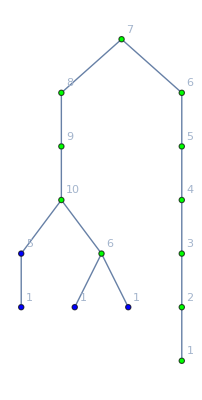

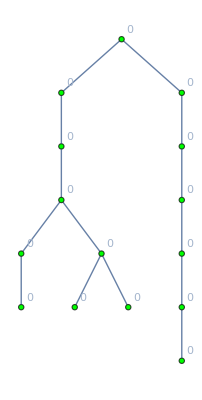
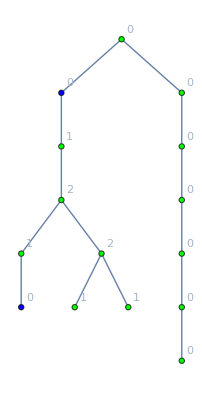
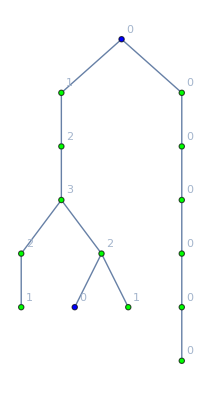
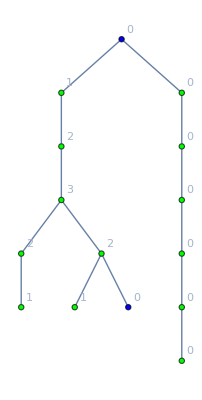
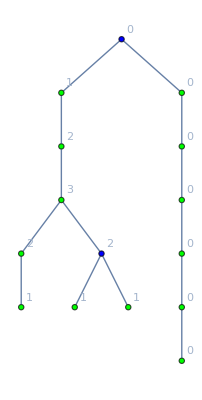
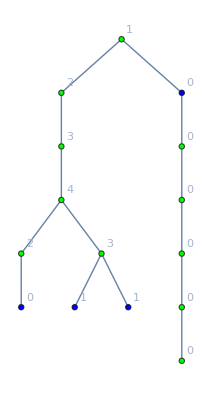
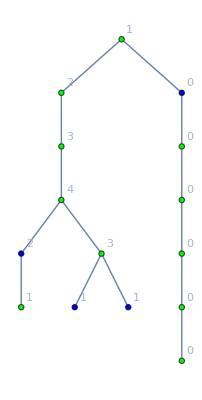
{(1 | {-Graphics-}
2 | {-Graphics-}
3 | {-Graphics-}
4 | {-Graphics-}
5 | {-Graphics-}
6 | {-Graphics-}
7 | {-Graphics-}
8 | {-Graphics-}
9 | {-Graphics-}
10 | {-Graphics-}
11 | {-Graphics-}
12 | {-Graphics-}
13 | {-Graphics-}
14 | {-Graphics-}
15 | {-Graphics-}
16 | {-Graphics-}
17 | {-Graphics-}
18 | {-Graphics-}
19 | {-Graphics-}
20 | {-Graphics-}
21 | {-Graphics-}
22 | {-Graphics-}),-Graphics-}

```mathematica
{({{-2, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -2, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -2, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {1, 1, 0, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -2}}),{1,1,5,6,10,9,8,7,6,5,4,3,2,1,1}}//fissionDecay
```